## Survival Distribution Simulations

This notebook numerically generates survival distributions under different models. These distributions are saved in the .h5 format to be imported by python.

This notebook requires the feature-rbsim branch of the quantum-utils-mathematica library: 
https://github.com/QuantumUtils/quantum-utils-mathematica/tree/feature-rbsim

```mathematica
Needs["QuantumUtils`"]
Needs["RBSim`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
mlist={1,100,200,500,1000,2000,5000,10000,20000,50000};
```

## Decay Rate Functions

Functions from Theorem 3 of https://arxiv.org/pdf/1703.09835.pdf to compute the decay rates of an RB curve for gate dependent noise.

```mathematica
Gu[chan_]:=With[{d=InputDim@chan},Super[FunctionChannel[chan[#-Tr[#]/d]&,InputDim->d],Basis->"Pauli"]]
```

```mathematica
p[gs_]:=Abs@First@Eigenvalues[
First@Super[
Sum[Gu[Unitary@GateUnitary[gs][i]]⊗Super[GateChannel[gs][i],Basis->"Pauli"],{i,Size@gs}]/Size[gs],
Basis->"Pauli"
],
1
]
t[gs_]:=Abs@First@Eigenvalues[First@Super[Sum[GateChannel[gs][i],{i,Size@gs}]/Size[gs]],1]
```

Average gate fidelity of the depolarizing channel with p[gs] and t[gs]:

```mathematica
F[gs_]:=Module[{d=InputDim@GateChannel[gs][1],dep},
dep=Super[FunctionChannel[p[gs](#-Tr[#]IdentityMatrix[d]/d)+ t[gs]Tr[#]IdentityMatrix[d]/d&,InputDim->d]];
AverageGateFidelity[dep]
]
```

```mathematica
Solve[p==(d F-1)/(d-1),F]
```

{{F→(1-p+d p)/d}}

## Depolarizing Error Model

```mathematica
depolarizingGate[p_]:=Super[FunctionChannel[(1-p)#+p Tr[#]/2&,InputDim->2]]
gateNoise=IndependentNoise[depolarizingGate[0.0002]];
gateChannels=Unitary[GateUnitary[$gaussianQubitGateSet][#]].First[gateNoise]&/@Range[12];

gs=GateNoiseGateSet[
GateSetName->"Depolarizing Noise",
Size->12,
Dimension->2,
GateProduct->GateProduct[$gaussianQubitGateSet],
GateInverse->GateInverse[$gaussianQubitGateSet],
GateUnitary->GateUnitary[$gaussianQubitGateSet],
GateNoise->gateNoise,
GateChannel->(gateChannels[[Last[{##}]]]&),
GateNoiseMemoryDepth->1
];
{p[gs],t[gs],1-F[gs]}
```

{0.9998,1.,0.0001}

```mathematica
protocol=RBProtocol[mlist,5000,1,TP[U],0.99TP[U]];
survivals=SimulateProtocol[gs,protocol,SimulationExportName->"../data/depolarizing_model_survivals"];
```

Saved ../data/depolarizing_model_survivals.h5

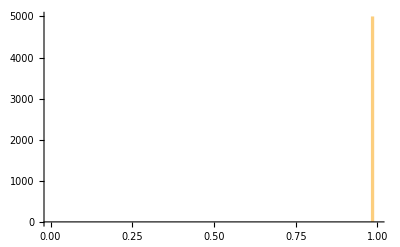
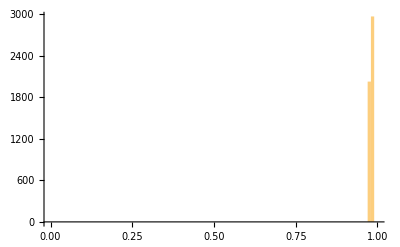
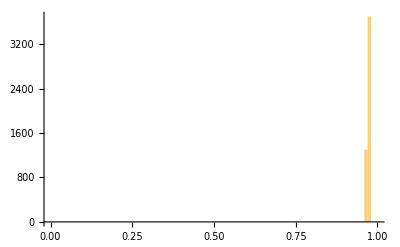
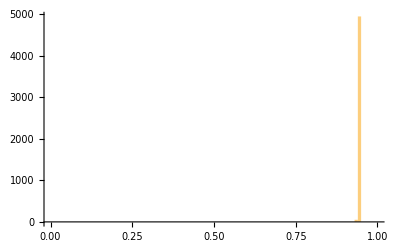
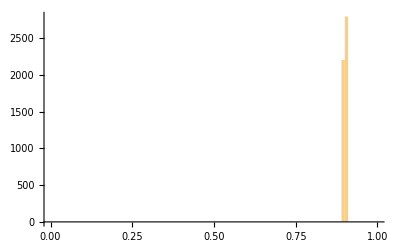
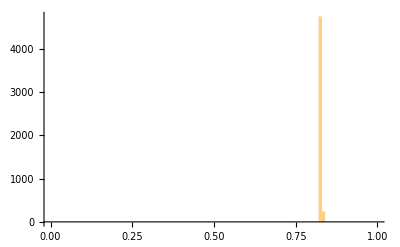
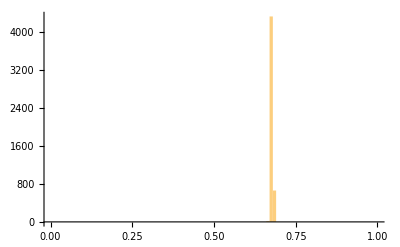
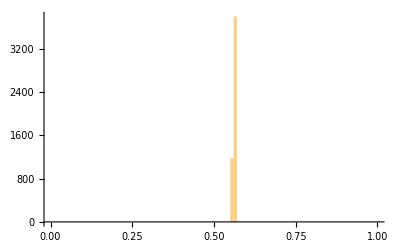

```mathematica
Histogram[#,{0,1,0.01},ImageSize->400]&/@survivals[[All,1,All,1]]
```

## Overrotation Error Model

```mathematica
gateChannels=Table[
If[DiagonalMatrixQ[GateUnitary[$gaussianQubitGateSet][i]],
Super@Unitary@GateUnitary[$gaussianQubitGateSet][i],
Super@Unitary[MatrixPower[GateUnitary[$gaussianQubitGateSet][i],1.011132]]
],
{i,12}
];
gateNoise=Table[Unitary[GateUnitary[$gaussianQubitGateSet][i]†].gateChannels[[i]],{i,12}];
gs=GateNoiseGateSet[
GateSetName->"Overrotation Noise",
Size->12,
Dimension->2,
GateProduct->GateProduct[$gaussianQubitGateSet],
GateInverse->GateInverse[$gaussianQubitGateSet],
GateUnitary->GateUnitary[$gaussianQubitGateSet],
GateNoise->(gateNoise[[Last[{##}]]]&),
GateChannel->(gateChannels[[Last[{##}]]]&),
GateNoiseMemoryDepth->1
];
{p[gs],t[gs],1-F[gs]}
```

{0.9998,1.,0.0001}

```mathematica
protocol=RBProtocol[mlist,5000,1,TP[U],0.99TP[U]];
survivals=SimulateProtocol[gs,protocol,SimulationExportName->"../data/overrotation_model_survivals"];
```

Saved ../data/overrotation_model_survivals.h5

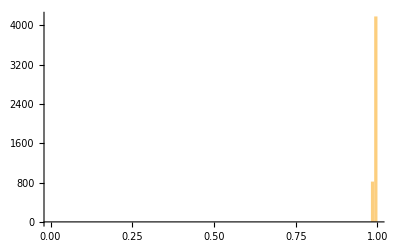
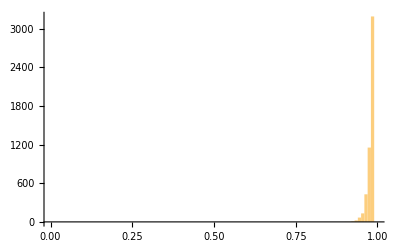
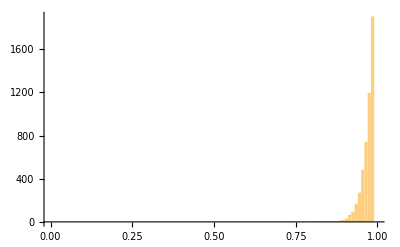
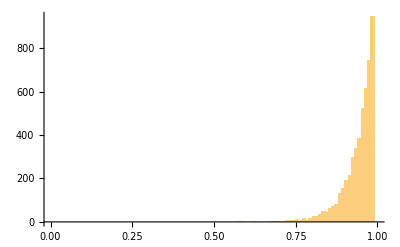
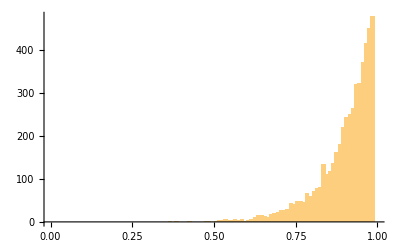
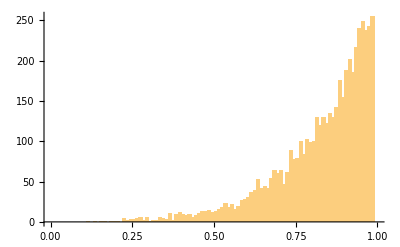
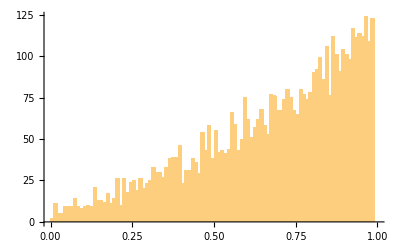
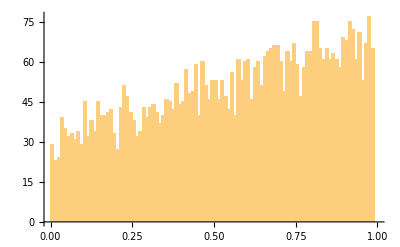

```mathematica
Histogram[#,{0,1,0.01},ImageSize->400]&/@survivals[[All,1,All,1]]
```

## Overrotation with Dephasing Error Model

```mathematica
dephasingGate[p_]:=Kraus[{Sqrt[1-p]TP[I],Sqrt[p]TP[Z]}]
gateChannels=Table[
If[DiagonalMatrixQ[GateUnitary[$gaussianQubitGateSet][i]],
Super@Unitary@GateUnitary[$gaussianQubitGateSet][i],
Super@Unitary[MatrixPower[GateUnitary[$gaussianQubitGateSet][i],1.01]]
].dephasingGate[0.000028954],
{i,12}
];
gateNoise=Table[Unitary[GateUnitary[$gaussianQubitGateSet][i]†].gateChannels[[i]],{i,12}];

gs=GateNoiseGateSet[
GateSetName->"Overrotation+Dephasing Noise",
Size->12,
Dimension->2,
GateProduct->GateProduct[$gaussianQubitGateSet],
GateInverse->GateInverse[$gaussianQubitGateSet],
GateUnitary->GateUnitary[$gaussianQubitGateSet],
GateNoise->(gateNoise[[Last[{##}]]]&),
GateChannel->(gateChannels[[Last[{##}]]]&),
GateNoiseMemoryDepth->1
];
{p[gs],t[gs],1-F[gs]}
```

{0.9998,1.,0.0001}

```mathematica
protocol=RBProtocol[mlist,5000,1,TP[U],0.99TP[U]];
survivals=SimulateProtocol[gs,protocol,SimulationExportName->"../data/overrotation_and_dephasing_model_survivals"];
```

Saved ../data/overrotation_and_dephasing_model_survivals.h5

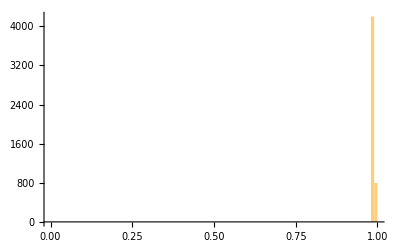
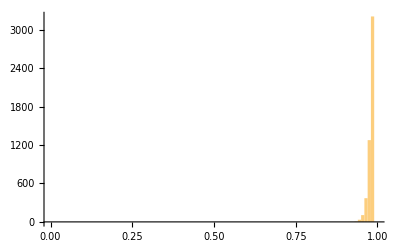
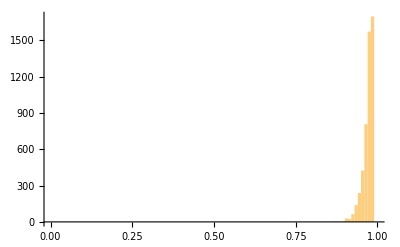
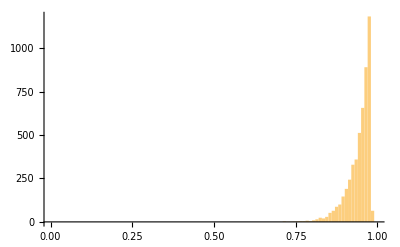
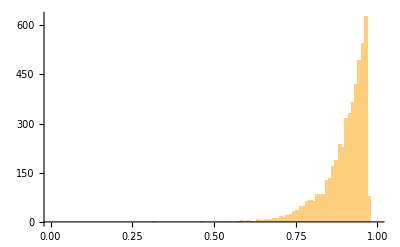
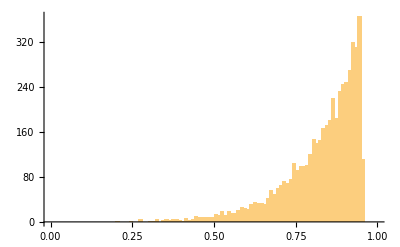
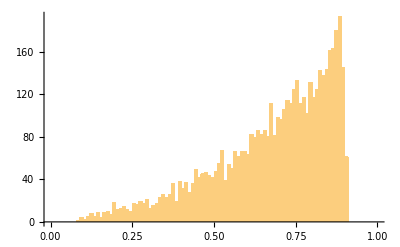
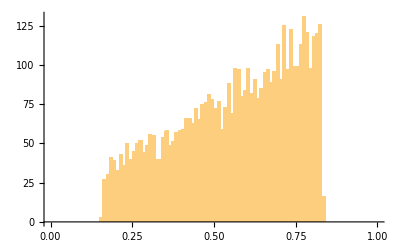

```mathematica
Histogram[#,{0,1,0.01},ImageSize->400]&/@survivals[[All,1,All,1]]
```

## Pathological Error Model

```mathematica
ρr=Unitary[MatrixExp[-I 0.1(TP[X]+TP[Y])/2]][TP[U]];
resetGate=Super@FunctionChannel[Tr[#]ρr&,InputDim->2];
otherGate=With[{p=0.01},Super@FunctionChannel[p Tr[#]TP[I]/2+(1-p) #&,InputDim->2]];
(*otherGate=With[{p=0.01},Super@Kraus[{Sqrt[1-p]TP[I],Sqrt[p]RandomUnitary[2]}]];*)
totalGate=With[{p=0.9},p resetGate+(1-p) otherGate];
gateNoise=IndependentNoise[totalGate];
gateChannels=Unitary[GateUnitary[$gaussianQubitGateSet][#]].First[gateNoise]&/@Range[12];

gs=GateNoiseGateSet[
GateSetName->"Multimodal survival distributions",
Size->12,
Dimension->2,
GateProduct->GateProduct[$gaussianQubitGateSet],
GateInverse->GateInverse[$gaussianQubitGateSet],
GateUnitary->GateUnitary[$gaussianQubitGateSet],
GateNoise->gateNoise,
GateChannel->(gateChannels[[Last[{##}]]]&),
GateNoiseMemoryDepth->1
];

protocol=RBProtocol[{1,2,5,20,50,100},5000,1,TP[U],0.99TP[U]];
survivals=SimulateProtocol[gs,protocol,SimulationExportName->"../data/pathological_model_survivals"];
```

Saved ../data/pathological_model_survivals.h5

```mathematica
{p[gs],t[gs],1-F[gs]}
```

{0.099,1.,0.4505}

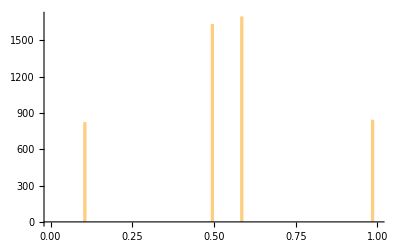
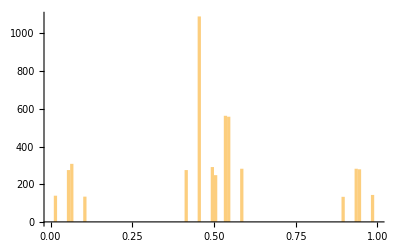
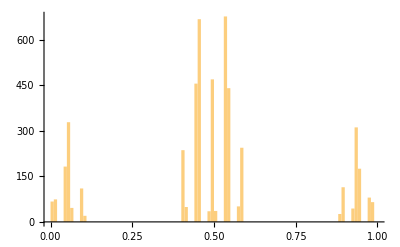
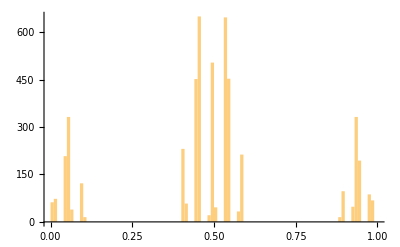
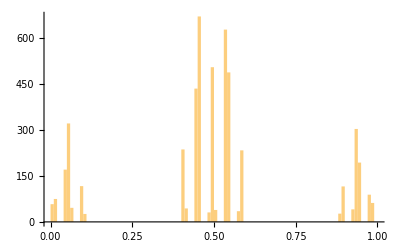
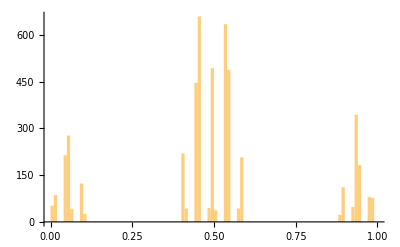

```mathematica
Histogram[#,{0,1,0.01},ImageSize->400]&/@survivals[[All,1,All,1]]
ListPlot[{Flatten@#,ConstantArray[1,Length@Flatten@#]}ᵀ,Filling->Axis,ImageSize->400,PlotRange->{{0,1},{0,1.5}}]&/@survivals
```

## X/2 Only

These are the necessary amplitudes (in MHz) for each of 10 1ns pulses steps to get a perfect π/2 rotation about x:

```mathematica
rawPulse=GaussianTailsPulse[0.001,0.01,0.005,Area->1/4]
X2unitary=Last@Unitaries@PulseSim[2π 0*TP[Z]/2,{rawPulse,{2π TP[X]/2,2π TP[Y]/2}}]//Chop;
X2unitary//MatrixForm
```

{{0.001,0.25872,0.},{0.001,1.56516,0.},{0.001,6.60608,0.},{0.001,19.4528,0.},{0.001,39.9644,0.},{0.001,57.2822,0.},{0.001,57.2822,0.},{0.001,39.9644,0.},{0.001,19.4528,0.},{0.001,6.60608,0.},{0.001,1.56516,0.}}

(0.707107 | 0.-0.707107 ⅈ
0.-0.707107 ⅈ | 0.707107)

```mathematica
ClearAll@X2channel;
X2channel[ϵmean_,ϵstd_,δωmean_,δωstd_,T2_]:=X2channel[ϵmean,ϵstd,δωmean,δωstd]=Module[{δω,ϵ},
Last@Superoperators@PulseSim[
LindbladForm[2π δω*TP[Z]/2,{1/Sqrt[T2]TP[Z]/2}],
{rawPulse,ϵ{2π TP[X]/2,2π TP[Y]/2}},
RandomMultinormalParameterDistribution[{ϵmean,δωmean},DiagonalMatrix[{ϵstd,δωstd}^2],{ϵ,δω},100]
]
]
```

```mathematica
X2choice=X2channel[1.001,0.01,0.001,0.01,100];
Re@AverageGateFidelity[Unitary[X2choice],example]
```

Re[AverageGateFidelity[Super[{{0.498938+9.11816×10^-23 ⅈ,0.0000351969-0.499913 ⅈ,0.0000351969+0.499913 ⅈ,0.501062+4.27043×10^-22 ⅈ},{0.0000300426-0.499916 ⅈ,0.498901+0.0000657632 ⅈ,0.501044-5.11305×10^-6 ⅈ,-0.0000300426+0.499916 ⅈ},{0.0000300426+0.499916 ⅈ,0.501044+5.11305×10^-6 ⅈ,0.498901-0.0000657632 ⅈ,-0.0000300426-0.499916 ⅈ},{0.501062-3.32949×10^-22 ⅈ,-0.0000351969+0.499913 ⅈ,-0.0000351969-0.499913 ⅈ,0.498938+1.61246×10^-22 ⅈ}},<params>],example]]

```mathematica
group=Dot@@@(Reverse/@{W[],W[X2,X2],W[Z2,X2],W[Z2,X2,Z],W[ZM2,X2,Z],W[Z,X2,Z2],W[ZM2,X2],W[X2,ZM2],W[Z,X2,ZM2],W[X2,Z2],W[X2,X2,Z],W[Z]}/.W[]->Id);
gateChannels=Super/@(group/.{
X2->X2channel[1.001,0.01,0.001,0.01,100],
Z2->Unitary[MatrixExp[-I (π/2)TP[Z]/2]],
Z->Unitary[MatrixExp[-I (π)TP[Z]/2]],
ZM2->Unitary[MatrixExp[I (π/2)TP[Z]/2]],
Id->Unitary[IdentityMatrix[2]]
});
gateUnitaries=First/@(group/.{
X2->Unitary[MatrixExp[-I (π/2)TP[X]/2]],
Z2->Unitary[MatrixExp[-I (π/2)TP[Z]/2]],
Z->Unitary[MatrixExp[-I (π)TP[Z]/2]],
ZM2->Unitary[MatrixExp[I (π/2)TP[Z]/2]],
Id->Unitary[IdentityMatrix[2]]
});
gateNoises=Super[Unitary[#2†].#1]&@@@({gateChannels,gateUnitaries}ᵀ);
```

```mathematica
GateProduct[$gaussianQubitGateSet]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{2,4,6,1,8,9,11,12,3,7,10,5},{3,5,1,7,2,10,4,9,8,6,12,11},{4,1,9,2,12,3,10,5,6,11,7,8},{5,7,10,3,9,8,12,11,1,4,6,2},{6,8,2,11,4,7,1,3,12,9,5,10},{7,3,8,5,11,1,6,2,10,12,4,9},{8,11,7,6,3,12,5,10,2,1,9,4},{9,12,4,10,1,11,2,6,5,3,8,7},{10,9,5,12,7,4,3,1,11,8,2,6},{11,6,12,8,10,2,9,4,7,5,1,3},{12,10,11,9,6,5,8,7,4,2,3,1}}⟦#1,#2⟧&

```mathematica
?GateChannel
```

TagBox[StyleBox["GateChannel", "Input", Rule[FontFamily, "Courier"]], DisplayForm] is a TagBox[StyleBox["GateNoiseGateSet", "Input", Rule[FontFamily, "Courier"]], DisplayForm] key storing a function  TagBox[StyleBox["f[", "Input", Rule[FontFamily, "Courier"]], DisplayForm]TagBox[StyleBox["i1", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm]TagBox[StyleBox[",", "Input", Rule[FontFamily, "Courier"]], DisplayForm]TagBox[StyleBox["i2", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm]TagBox[StyleBox[",", "Input", Rule[FontFamily, "Courier"]], DisplayForm]TagBox[StyleBox["...", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm]TagBox[StyleBox[",", "Input", Rule[FontFamily, "Courier"]], DisplayForm]TagBox[StyleBox["in", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm]TagBox[StyleBox["]", "Input", Rule[FontFamily, "Courier"]], DisplayForm] that returns an object satisfying TagBox[StyleBox["ChannelPulseQ", "Input", Rule[FontFamily, "Courier"]], DisplayForm] given the gate index history TagBox[StyleBox["i1,i2,...,in", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm] where TagBox[StyleBox["in", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm] is the most recent. This channel is the composition of the ideal gate TagBox[StyleBox["GateUnitary", "Input", Rule[FontFamily, "Courier"]], DisplayForm] with index TagBox[StyleBox["in", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm] followed by the TagBox[StyleBox["GateNoise", "Input", Rule[FontFamily, "Courier"]], DisplayForm] error, where the TagBox[StyleBox["GateNoise", "Input", Rule[FontFamily, "Courier"]], DisplayForm] is allowed to depend on the indicesTagBox[StyleBox[" i1,i2,...,i(n-1)", "Input", Rule[FontFamily, "Courier"], Rule[FontWeight, "Plain"], Rule[FontSlant, "Italic"]], DisplayForm] that preceded the current gate.

```mathematica
TestGateSetProducts
```

```mathematica
gs=GateNoiseGateSet[
GateSetName->"Depolarizing Noise",
Size->12,
Dimension->2,
GateProduct->GateProduct[$gaussianQubitGateSet],
GateInverse->GateInverse[$gaussianQubitGateSet],
GateUnitary->(gateUnitaries[[Last[{##}]]]&),
GateNoise->gateNoise,
GateChannel->(gateChannels[[Last[{##}]]]&)
];
```

```mathematica
TestGateSetProducts[gs]
```

{{1,1,1,1,1,1,1,1,1,1,1,1},{1,1/4,1/4,1/4,1/4,0,1/4,1/4,1/4,1/4,1/4,1/4},{1,1,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4},{1,1/4,0,1/4,1/4,1/4,0,1/4,1/4,0,0,1/4},{1,0,0,1/4,0,1/4,1/4,0,0,1/4,1/4,1/4},{1,0,0,0,1/4,1/4 Abs[-((1-ⅈ) ⅇ^(-(ⅈ π)/4))/(√2)-((1+ⅈ) ⅇ^((ⅈ π)/4))/(√2)]^2,0,1/4 Abs[-((1-ⅈ) ⅇ^(-(ⅈ π)/4))/(√2)-((1+ⅈ) ⅇ^((ⅈ π)/4))/(√2)]^2,1/4,1/4,1/4,0},{1,0,1/4 Abs[((1-ⅈ) ⅇ^(-(ⅈ π)/4))/(√2)+((1+ⅈ) ⅇ^((ⅈ π)/4))/(√2)]^2,1/4,1/4,0,1/4 Abs[-((1-ⅈ) ⅇ^(-(ⅈ π)/4))/(√2)-((1+ⅈ) ⅇ^((ⅈ π)/4))/(√2)]^2,1,1/4,0,0,1/4},{1,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,0,1/4},{1,1/4,1/4,1/4,0,1/4,0,1/4,0,1,0,1/4},{1,0,1/4,0,1/4,0,1/4,1/4,1/4,1/4,1/4,0},{1,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1,1/4},{1,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1}}

```mathematica
nm=NoiseModel[
DistortionOperator->FastExponentialDistortion[0.003,10,0],
DistortionMultiplier->10,
GateNoise->IndependentNoise[Kraus[{Sqrt[0.9999] TP[I],Sqrt[0.0001] TP[Z]}]]
];
gs=CompileGateNoise[$gaussianQubitGateSet,nm,2]
```

GateNoiseGateSet[GateSetName→"Gaussian 2-design on Qubits",Dimension→2,Size→12,...]

```mathematica
protocol=RBProtocol[{1,10,50,100,500,1000,1500,2000,3000,5000,10000,20000},100,1,TP[U],TP[U]];
survivals=SimulateProtocol[gs,protocol,SimulationExportName->"../data/high_fidelity"];
```

Saved ../data/high_fidelity.h5

{0.982912,0.499974,0.999843}

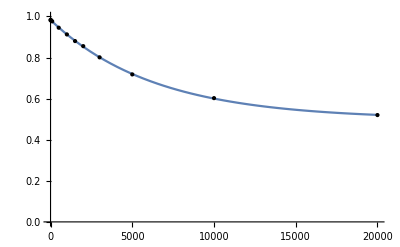

```mathematica
model=(A-B)p^m+B;
normalizedSurvivals={SequenceLengths[protocol],Total[survivals[[All,1,All,1]],{2}]/100}ᵀ;
fit=FindFit[normalizedSurvivals,{model,0<p<1,0<A<1,0<B<1},{A,B,p},m];
modelf=Function[{m},Evaluate[model/.fit]];
Print[{A,B,p}/.fit];
Plot[modelf[m],{m,0,20000},Epilog->Map[Point,normalizedSurvivals],PlotRange->{All,{0,1}}]
```

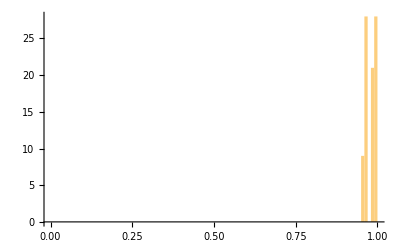
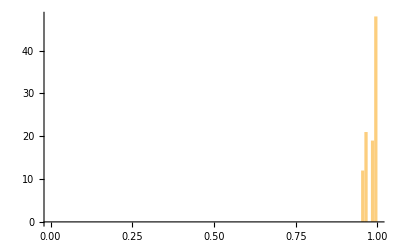
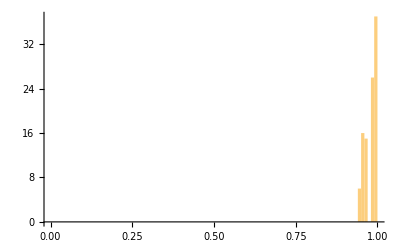
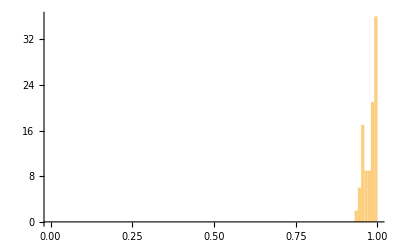
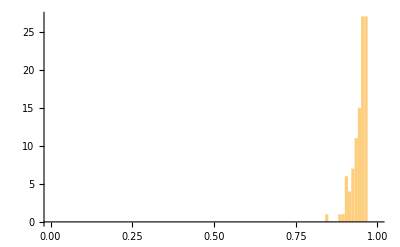
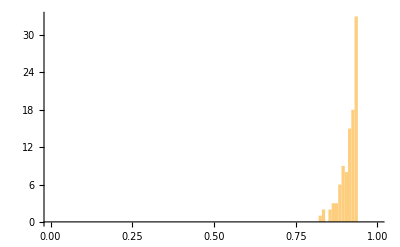
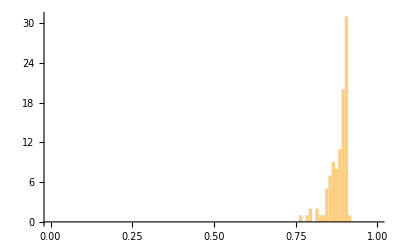
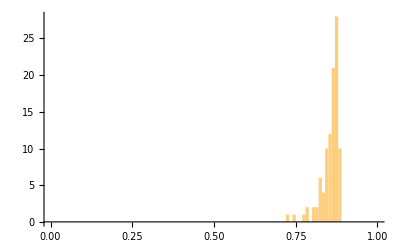

```mathematica
Histogram[#,{0,1,0.01},ImageSize->400]&/@survivals[[All,1,All,1]]
```

## For LRB

```mathematica
Dij[i_,j_,d1_,d2_]:=Module[{Ii,d=d1+d2},
If[i==1,
Ii=DiagonalMatrix[Join[ConstantArray[1/d1,d1],ConstantArray[0,d2]]];,
Ii=DiagonalMatrix[Join[ConstantArray[0,d1],ConstantArray[1/d2,d2]]];
];
If[j==1,
Super@FunctionChannel[Total[Diagonal[#][[;;d1]]]Ii&,InputDim->d],
Super@FunctionChannel[Total[Diagonal[#][[d1+1;;]]]Ii&,InputDim->d]
]
]
L[ρ_,d1_]:=1-Total[Diagonal[ρ][[;;d1]]]
L1[E_,d1_]:=Module[{I1,d2=InputDim@E-d1},
I1=DiagonalMatrix[Join[ConstantArray[1,d1],ConstantArray[0,d2]]];
L[E[I1/d1],d1]
]
L2[E_,d1_]:=Module[{I2,d2=InputDim@E-d1},
I2=DiagonalMatrix[Join[ConstantArray[0,d1],ConstantArray[1,d2]]];
1-L[E[I2/d2],d1]
]
F1[E_,d1_]:=Module[{d2=InputDim@E-d1,I1,Fpro},
I1=Join[ConstantArray[1,d1],ConstantArray[0,d2]];
Fpro=Total[(I1⊗I1)*Diagonal[First@Super@E]]/d1^2;
(d1 Fpro+1-L1[E,d1])/(d1+1)
]
```

Here is the depolarizing leakage extension (DLE) for a map E acting only on space 1.

```mathematica
AddIdentity[K_List,dim_]:=BlockMatrix[K,0*IdentityMatrix[dim]]
AddIdentity[E_,dim_]:=Module[{all=First@Kraus[E],Ks,Ls},
Super@If[Length@Dimensions@all==3,
Kraus[AddIdentity[#,dim]&/@all],
Kraus[{AddIdentity[#,dim]&/@all[[1]],AddIdentity[#,dim]&/@all[[2]]}]
]
]
DLE[E_,L1_,L2_,d2_]:=With[{d1=InputDim@E},(1-L1)AddIdentity[E,d2]+L1 Dij[2,1,d1,d2]+L2 Dij[1,2,d1,d2]+(1-L2)Dij[2,2,d1,d2]]
```

Now set up a gate set with gate independent noise

```mathematica
dephasingGate[p_]:=Kraus[{Sqrt[1-p]TP[I],Sqrt[p]TP[Z]}]
unitaryGate:=Unitary[MatrixExp[-I (0.1π/180)TP[Z]/2]]
gateNoise=DLE[dephasingGate[0.003].unitaryGate,0.001,0.0015,1];
Re@{F1[gateNoise,2],L1[gateNoise,2],L2[gateNoise,2]}

gateUnitaries=BlockMatrix[GateUnitary[$gaussianQubitGateSet][#],{{1}}]&/@Range[12];
gateChannels=Super[Unitary[#].gateNoise]&/@gateUnitaries;

gs=GateNoiseGateSet[
GateSetName->"Z+Dephasing with L1 and L2 leakage",
Size->12,
Dimension->2,
GateProduct->GateProduct[$gaussianQubitGateSet],
GateInverse->GateInverse[$gaussianQubitGateSet],
GateUnitary->(gateUnitaries[[Last[{##}]]]&),
GateNoise->IndependentNoise[gateNoise],
GateChannel->(gateChannels[[Last[{##}]]]&),
GateNoiseMemoryDepth->1
];
```

{0.997001,0.001,0.0015}

```mathematica
LRBProtocol[seqLengths_,numSeqs_,shotsPerSeq_,ρlist_,Mlist_]:=Module[{seqGen,gateSim},
	(* Use two closures to make sure every shot of the same (seqLength,seqNum) is identical *)
	seqGen[gs_,{seqLength_,_,seqNum_}] :=RBDraw[gs, seqLength];
	gateSim[gs_GateNoiseGateSet,{idxs__}] := With[{
op=Fold[
(First[Super[GateChannel[gs][#2]]].#1)&,
Join[Sequence@@(Vec/@ρlist),2],
 {idxs}
]},
Re[(Flatten[Vec[#]]&/@Mlist).op]
];
	Protocol[
		ProtocolName -> "Randomized Benchmarking",
		SequenceLengths -> seqLengths,
		ExperimentTypes -> ({0}&),
		NumSequenceDraws -> (numSeqs&),
		NumRepetitions -> (shotsPerSeq&),
		SequenceGenerator -> seqGen,
		SimulationOptions -> NotImplemented[],
		SimulationParser -> (Observables[#][[All,-1]]&),
		GateSimulator -> gateSim,
		ParallelOptions -> {Method->"CoarsestGrained"},
		TotalGates -> (shotsPerSeq * numSeqs * Total[seqLengths+1])
	]
]
```

```mathematica
mlist={1,10,50,100,200,300,500,1000,1500,2000,3000,4000};
protocol=LRBProtocol[mlist,100,1,{Projector[{0.9999,0,0}],Projector[{0,0.9995,0}]},{Projector[{0.99999,0,0}],Projector[{0,0.999,0}]}];
survivals=SimulateProtocol[gs,protocol,SimulationExportName->"../data/lrb-dephasing_z_andL1L2"];
```

Saved ../data/lrb-dephasing_z_andL1L2.h5

```mathematica
survivals//Dimensions
```

{9,1,500,1,2,2}

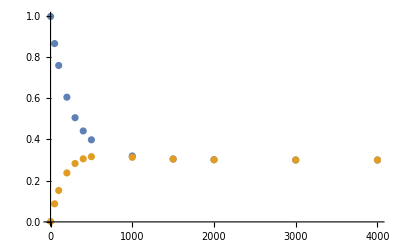

```mathematica
ListPlot[{
{mlist,Mean/@survivals[[All,1,All,1,1,1]]}ᵀ,
{mlist,Mean/@survivals[[All,1,All,1,1,2]]}ᵀ
}]
```

```mathematica
MatrixPower[GateChannel[gs][1],50000][DiagonalMatrix[{0,0,1}]]//Chop//MatrixForm
```

(0.3 | 0 | 0
0 | 0.3 | 0
0 | 0 | 0.4)

```mathematica
GateChannel[gs][6]//TracePreservingQ
dephasingGate[0.001]//TracePreservingQ
```

True

True

## Nonmarkovian

```mathematica
nmm[J_,T2_,T2env_]:=NoiseModel[
Generator->LindbladForm[2π J TP[ZZ]/4+TP[IX],{Sqrt[1/T2]TP[ZI],Sqrt[1/T2env]TP[IZ]}]
]
```

```mathematica
rawPulseX2=GaussianTailsPulse[0.001,0.01,0.005,Area->1/4];
rawPulseY2=FromPulse@PulsePhaseRotate[ToPulse@rawPulseX2,π/2];
rawPulseXM2=FromPulse@PulsePhaseRotate[ToPulse@rawPulseX2,π];
rawPulseYM2=FromPulse@PulsePhaseRotate[ToPulse@rawPulseX2,-π/2];
group=List@@@(Reverse/@{W[],W[X2,X2],W[X2,Y2],W[XM2,Y2],W[XM2,YM2],W[YM2,XM2],W[X2,YM2],W[Y2,X2],W[Y2,XM2],W[YM2,X2],W[Y2,Y2],W[X2,X2,Y2,Y2]}/.W[]->W[Id]);
gatePulses={Join@@Reverse[#],{2π TP[X]/2,2π TP[Y]/2}}&/@(group/.{
X2->rawPulseX2,
Y2->rawPulseY2,
XM2->rawPulseXM2,
YM2->rawPulseYM2,
Id->{{$MachineEpsilon,0,0}}
});
gateUnitaries=Dot@@@(group/.{
X2->MatrixExp[-I (π/2)TP[XI]/2],
Y2->MatrixExp[-I (π/2)TP[YI]/2],
XM2->MatrixExp[I (π/2)TP[XI]/2],
YM2->MatrixExp[I (π/2)TP[YI]/2],
Id->IdentityMatrix[4]
});
mulTable={{1,2,3,4,5,6,7,8,9,10,11,12},{2,1,4,3,7,8,5,6,10,9,12,11},{3,5,6,9,10,1,8,11,12,2,7,4},{4,7,8,10,9,2,6,12,11,1,5,3},{5,3,9,6,8,11,10,1,2,12,4,7},{6,10,1,12,2,3,11,7,4,5,8,9},{7,4,10,8,6,12,9,2,1,11,3,5},{8,9,2,11,1,4,12,5,3,7,6,10},{9,8,11,2,12,5,1,4,7,3,10,6},{10,6,12,1,11,7,2,3,5,4,9,8},{11,12,5,7,3,9,4,10,6,8,1,2},{12,11,7,5,4,10,3,9,8,6,2,1}};
invTable={1,2,6,10,8,3,9,5,7,4,11,12};
gs=GateSet[
GateSetName->"coupled to second qubit",
Size->12,
Dimension->4,
GateProduct->(mulTable[[#1,#2]]&),
GateInverse->(invTable[[#]]&),
GateUnitary->(gateUnitaries[[#]]&),
GatePulse->(gatePulses[[#]]&)
]
```

GateSet[GateSetName→"coupled to second qubit",Dimension→4,Size→12,...]

```mathematica
mlist=Round[10^Table[m,{m,0,3,0.3}]];
```

```mathematica
mlist
```

{1,2,4,8,16,32,63,126,251,501,1000}

```mathematica
gngs=CompileGateNoise[$gaussianQubitGateSet,nmm[0.9,100,1000],1];
protocol=RBProtocol[mlist,50,1,TP[UI]/2,0.99TP[UI]];
survivals=SimulateProtocol[gngs,protocol,SimulationExportName->"../data/nonmarkovian"];
```

Saved ../data/nonmarkovian.h5

{0.990017,0.513572,0.995729}

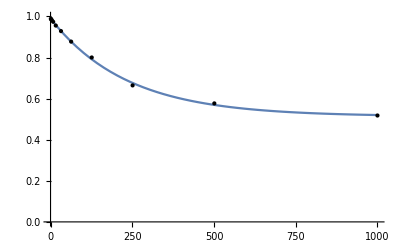

```mathematica
model=(A-B)p^m+B;
normalizedSurvivals={SequenceLengths[protocol],Total[survivals[[All,1,All,1]],{2}]/NumSequenceDraws[protocol][]}ᵀ;
fit=FindFit[normalizedSurvivals,{model,0<p<1,0<A<1,0<B<1},{A,B,p},m];
modelf=Function[{m},Evaluate[model/.fit]];
Print[{A,B,p}/.fit];
Plot[modelf[m],{m,0,Max@SequenceLengths@protocol},Epilog->Map[Point,normalizedSurvivals],PlotRange->{All,{0,1}}]
```